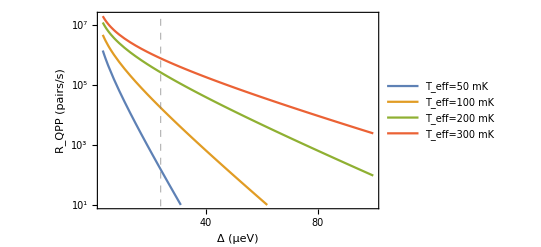

```mathematica
(* Panel C of Figure 2 of the main text *)
(* plot of rate of quasiparticle pair excitation versus gap at a fixed TLF effective temperature *)

(* these plots do not include the effects of the high attempt frequency of the TLFs; the quasiparticle excitation is exponentially suppressed by the factor $2 Delta/k_B T_eff $, where the rate of TLF transitions Gamma is set to k_B T_eff/hbar,  T_eff is the effective temperature of the TLF's, and $Delta$ is the topological gap)  *)

(* all calculations are done in units of gigahertz and microns *)
(* conversions are 1 μeV = 0.0116 K, 1 μeV = 0.2418 GHz  *)
ClearAll["Global`*"];

mykT=.;
mykTinmK=.;
myDelta=.;
myDeltainmicrovolts=.;
myGamma0=.;

length=3. ;        (* length = 3 microns *)
deltamu=0.138;(* deltamu is in GHz *)
(* prefactor=(length/16)*(deltamu)^2/vFermi this is prefactor in units of ns *)
(* let's write prefactor in Hz: *)

(* Fermi velocity is gap-dependent.  The gap dependence of the value was estimated by requiring that the Majorana extend be about 0.25 microns, as per the discussion in the supplementary information. *)
vFermi[myDelta_]:=1.25*myDelta; (* vFermi = (0.75)(gap in GHz) microns/ns *)

(*prefactor of the pair excitation rate is a function of temperature and also of myDelta (in GHz) *)
prefactor[mykT_?NumericQ,myDelta_?NumericQ]:=(10^9*(length/16)*(deltamu)^2/vFermi[myDelta])*(mykT/1.04);


(* Note that the prefactor is proportional to T according to Dutta and Horn because density of epsilons (TLF asymmetries) is uniform and all the TLFs with epsilon \lessim kT are active.  We will assume that in Aghaee et al (Nature 2025) the TLF effective temperature T_eff is equal to the electron temperature, which is given as 0.05 K, so the prefactor has a factor of (T_eff/0.05 K) = (T_eff/1.04) when converted to GHz. *)

(* function that calculates the pair excitation rate *)(*rate[myGamma_?NumericQ,myDelta_?NumericQ,mykT_?NumericQ]:=prefactor[mykT,myDelta]*(myGamma/myDelta)*Exp[-Max[2*myDelta/mykT,myGamma/(2*myDelta)]]; *)
rate[myGamma_?NumericQ,myDelta_?NumericQ,mykT_?NumericQ]:=prefactor[mykT,myDelta]*(myGamma/myDelta)*Exp[-(2*myDelta/mykT+myGamma/(2*myDelta))];

maxRate[myDelta_?NumericQ,mykT_?NumericQ]:=NMaxValue[{rate[myGamma,myDelta,mykT],0<myGamma<2*myDelta},myGamma];

mykT=mykTinmK*0.0284; (* converts mK to GHz *)
myDelta=myDeltainmicrovolts*0.2418;  (* converts microeV to GHz *)(* will plot rate versus myDelta at different effective temperatures *)
(* *)
mykT=mykTinmK*0.0284; (* converts mK to GHz *)
myDelta=myDeltainmicrovolts*0.2418;  (* converts microeV to GHz *)

(* now plot rate versus myDelta at different effective temperatures *)
(* the function includes mygamma0, which is the attempt frequency, which is a relevant parameter for a specific model in which the TLFs are activated over a barrier, but in this program the parameter is set to 1. *)

LogPlot[{maxRate[myDelta,mykT]/.{mykTinmK->50},maxRate[myDelta,mykT]/.{mykTinmK->100},
maxRate[myDelta,mykT]/.{mykTinmK->200},
maxRate[myDelta,mykT]/.{mykTinmK->300}
},
{myDeltainmicrovolts,3,100},
Axes->False,Frame->True,FrameStyle->Black,BaseStyle->{FontSize->13.5,FontFamily->"Helvetica"},FrameLabel->{"Δ (μeV)","R_QPP (pairs/s)",None,None},
PlotRange->{{3,100},{10,2*10^7}},
FrameTicks->{{{{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"},{10^5,"10^5"},{10^6,"10^6"},{10^7,"10^7"}},None},{{0,20,40,60,80,100},None}},
(* put a grid line at the 90th percentile gap of 23.8 μeV *)
GridLines->{{23.8},None},
GridLinesStyle->Directive[Thick,Gray,Dashed],
 PlotLegends->Placed[{"\!\(\*SubscriptBox[\(T\), \(eff\)]\)=50 mK","\!\(\*SubscriptBox[\(T\), \(eff\)]\)=100 mK","\!\(\*SubscriptBox[\(T\), \(eff\)]\)=200 mK","\!\(\*SubscriptBox[\(T\), \(eff\)]\)=300 mK"},Right] 
] 
myDeltainmicrovolts=.;
```